```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

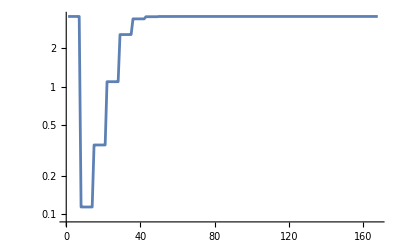

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.328×10^-7,R33→-0.319304,R34→5.×10^-10,maximizeMe→3.56618|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

Q2FFkG : 114.6453005197
Q1FFkG : -13.926389729
Q0FFkG : 166.7217584613
Q0DkG : -120.7521824003
Q1DkG : 148.0624497808
Q2DkG : -51.7600001869
R11 : 1.0827559173
R12 : -1.328e-7
R33 : -0.3193040774
R34 : 5.e-10
maximizeMe : 3.5661808648

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

√(Abs[Missing[KeyAbsent,PDrive_mean_x]-Missing[KeyAbsent,PWitness_mean_x]]^2+Abs[Missing[KeyAbsent,PDrive_mean_y]-Missing[KeyAbsent,PWitness_mean_y]]^2)

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

```mathematica
Length[raw]
Select[raw,Abs[1-#R11]<2&];

Export[
"~/srDataPartial.csv",
Dataset[Select[raw,Abs[1-#R11]<2&]]
]
```

168

{<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-4.91×10^-8,R33→-0.319304,R34→7.325×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-4.85×10^-8,R33→-0.319304,R34→7.327×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-4.86×10^-8,R33→-0.319304,R34→7.332×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-4.88×10^-8,R33→-0.319304,R34→7.341×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-4.66×10^-8,R33→-0.319304,R34→7.695×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-3.86×10^-8,R33→-0.319304,R34→7.466×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-4.35×10^-8,R33→-0.319304,R34→7.495×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.732,Q1FFkG→-13.9739,Q0FFkG→166.446,Q0DkG→-128.215,Q1DkG→147.12,Q2DkG→-54.3036,R11→0.147062,R12→-4.35389,R33→-5.32767,R34→-32.2097,maximizeMe→0.114301|>,<|Q2FFkG→114.732,Q1FFkG→-13.9739,Q0FFkG→166.446,Q0DkG→-128.215,Q1DkG→147.12,Q2DkG→-54.3036,R11→0.147062,R12→-4.35389,R33→-5.32767,R34→-32.2097,maximizeMe→0.114301|>,<|Q2FFkG→114.732,Q1FFkG→-13.9739,Q0FFkG→166.446,Q0DkG→-128.215,Q1DkG→147.12,Q2DkG→-54.3036,R11→0.147062,R12→-4.35389,R33→-5.32767,R34→-32.2097,maximizeMe→0.114301|>,<|Q2FFkG→114.732,Q1FFkG→-13.9739,Q0FFkG→166.446,Q0DkG→-128.215,Q1DkG→147.12,Q2DkG→-54.3036,R11→0.147062,R12→-4.35389,R33→-5.32767,R34→-32.2097,maximizeMe→0.114301|>,<|Q2FFkG→114.732,Q1FFkG→-13.9739,Q0FFkG→166.446,Q0DkG→-128.215,Q1DkG→147.12,Q2DkG→-54.3036,R11→0.147062,R12→-4.35389,R33→-5.32767,R34→-32.2097,maximizeMe→0.114301|>,<|Q2FFkG→114.732,Q1FFkG→-13.9739,Q0FFkG→166.446,Q0DkG→-128.215,Q1DkG→147.12,Q2DkG→-54.3036,R11→0.147062,R12→-4.35389,R33→-5.32767,R34→-32.2097,maximizeMe→0.114301|>,<|Q2FFkG→114.732,Q1FFkG→-13.9739,Q0FFkG→166.446,Q0DkG→-128.215,Q1DkG→147.12,Q2DkG→-54.3036,R11→0.147062,R12→-4.35389,R33→-5.32767,R34→-32.2097,maximizeMe→0.114301|>,<|Q2FFkG→114.671,Q1FFkG→-13.9407,Q0FFkG→166.639,Q0DkG→-122.996,Q1DkG→147.779,Q2DkG→-52.5249,R11→0.806055,R12→-1.29008,R33→-1.86315,R34→-9.92864,maximizeMe→0.350243|>,<|Q2FFkG→114.671,Q1FFkG→-13.9407,Q0FFkG→166.639,Q0DkG→-122.996,Q1DkG→147.779,Q2DkG→-52.5249,R11→0.806055,R12→-1.29008,R33→-1.86315,R34→-9.92864,maximizeMe→0.350243|>,<|Q2FFkG→114.671,Q1FFkG→-13.9407,Q0FFkG→166.639,Q0DkG→-122.996,Q1DkG→147.779,Q2DkG→-52.5249,R11→0.806055,R12→-1.29008,R33→-1.86315,R34→-9.92864,maximizeMe→0.350243|>,<|Q2FFkG→114.671,Q1FFkG→-13.9407,Q0FFkG→166.639,Q0DkG→-122.996,Q1DkG→147.779,Q2DkG→-52.5249,R11→0.806055,R12→-1.29008,R33→-1.86315,R34→-9.92864,maximizeMe→0.350243|>,<|Q2FFkG→114.671,Q1FFkG→-13.9407,Q0FFkG→166.639,Q0DkG→-122.996,Q1DkG→147.779,Q2DkG→-52.5249,R11→0.806055,R12→-1.29008,R33→-1.86315,R34→-9.92864,maximizeMe→0.350243|>,<|Q2FFkG→114.671,Q1FFkG→-13.9407,Q0FFkG→166.639,Q0DkG→-122.996,Q1DkG→147.779,Q2DkG→-52.5249,R11→0.806055,R12→-1.29008,R33→-1.86315,R34→-9.92864,maximizeMe→0.350243|>,<|Q2FFkG→114.671,Q1FFkG→-13.9407,Q0FFkG→166.639,Q0DkG→-122.996,Q1DkG→147.779,Q2DkG→-52.5249,R11→0.806055,R12→-1.29008,R33→-1.86315,R34→-9.92864,maximizeMe→0.350243|>,<|Q2FFkG→114.652,Q1FFkG→-13.93,Q0FFkG→166.701,Q0DkG→-121.315,Q1DkG→147.991,Q2DkG→-51.9518,R11→1.01376,R12→-0.321903,R33→-0.709444,R34→-2.50902,maximizeMe→1.09791|>,<|Q2FFkG→114.652,Q1FFkG→-13.93,Q0FFkG→166.701,Q0DkG→-121.315,Q1DkG→147.991,Q2DkG→-51.9518,R11→1.01376,R12→-0.321903,R33→-0.709444,R34→-2.50902,maximizeMe→1.09791|>,<|Q2FFkG→114.652,Q1FFkG→-13.93,Q0FFkG→166.701,Q0DkG→-121.315,Q1DkG→147.991,Q2DkG→-51.9518,R11→1.01376,R12→-0.321903,R33→-0.709444,R34→-2.50902,maximizeMe→1.09791|>,<|Q2FFkG→114.652,Q1FFkG→-13.93,Q0FFkG→166.701,Q0DkG→-121.315,Q1DkG→147.991,Q2DkG→-51.9518,R11→1.01376,R12→-0.321903,R33→-0.709444,R34→-2.50902,maximizeMe→1.09791|>,<|Q2FFkG→114.652,Q1FFkG→-13.93,Q0FFkG→166.701,Q0DkG→-121.315,Q1DkG→147.991,Q2DkG→-51.9518,R11→1.01376,R12→-0.321903,R33→-0.709444,R34→-2.50902,maximizeMe→1.09791|>,<|Q2FFkG→114.652,Q1FFkG→-13.93,Q0FFkG→166.701,Q0DkG→-121.315,Q1DkG→147.991,Q2DkG→-51.9518,R11→1.01376,R12→-0.321903,R33→-0.709444,R34→-2.50902,maximizeMe→1.09791|>,<|Q2FFkG→114.652,Q1FFkG→-13.93,Q0FFkG→166.701,Q0DkG→-121.315,Q1DkG→147.991,Q2DkG→-51.9518,R11→1.01376,R12→-0.321903,R33→-0.709444,R34→-2.50902,maximizeMe→1.09791|>,<|Q2FFkG→114.646,Q1FFkG→-13.927,Q0FFkG→166.718,Q0DkG→-120.849,Q1DkG→148.05,Q2DkG→-51.7929,R11→1.07093,R12→-0.0551828,R33→-0.38642,R34→-0.431625,maximizeMe→2.57181|>,<|Q2FFkG→114.646,Q1FFkG→-13.927,Q0FFkG→166.718,Q0DkG→-120.849,Q1DkG→148.05,Q2DkG→-51.7929,R11→1.07093,R12→-0.0551828,R33→-0.38642,R34→-0.431625,maximizeMe→2.57181|>,<|Q2FFkG→114.646,Q1FFkG→-13.927,Q0FFkG→166.718,Q0DkG→-120.849,Q1DkG→148.05,Q2DkG→-51.7929,R11→1.07093,R12→-0.0551828,R33→-0.38642,R34→-0.431625,maximizeMe→2.57181|>,<|Q2FFkG→114.646,Q1FFkG→-13.927,Q0FFkG→166.718,Q0DkG→-120.849,Q1DkG→148.05,Q2DkG→-51.7929,R11→1.07093,R12→-0.0551828,R33→-0.38642,R34→-0.431625,maximizeMe→2.57181|>,<|Q2FFkG→114.646,Q1FFkG→-13.927,Q0FFkG→166.718,Q0DkG→-120.849,Q1DkG→148.05,Q2DkG→-51.7929,R11→1.07093,R12→-0.0551828,R33→-0.38642,R34→-0.431625,maximizeMe→2.57181|>,<|Q2FFkG→114.646,Q1FFkG→-13.927,Q0FFkG→166.718,Q0DkG→-120.849,Q1DkG→148.05,Q2DkG→-51.7929,R11→1.07093,R12→-0.0551828,R33→-0.38642,R34→-0.431625,maximizeMe→2.57181|>,<|Q2FFkG→114.646,Q1FFkG→-13.927,Q0FFkG→166.718,Q0DkG→-120.849,Q1DkG→148.05,Q2DkG→-51.7929,R11→1.07093,R12→-0.0551828,R33→-0.38642,R34→-0.431625,maximizeMe→2.57181|>,<|Q2FFkG→114.645,Q1FFkG→-13.9265,Q0FFkG→166.721,Q0DkG→-120.763,Q1DkG→148.061,Q2DkG→-51.7638,R11→1.08139,R12→-0.00636934,R33→-0.327056,R34→-0.0498504,maximizeMe→3.41375|>,<|Q2FFkG→114.645,Q1FFkG→-13.9265,Q0FFkG→166.721,Q0DkG→-120.763,Q1DkG→148.061,Q2DkG→-51.7638,R11→1.08139,R12→-0.00636934,R33→-0.327056,R34→-0.0498504,maximizeMe→3.41375|>,<|Q2FFkG→114.645,Q1FFkG→-13.9265,Q0FFkG→166.721,Q0DkG→-120.763,Q1DkG→148.061,Q2DkG→-51.7638,R11→1.08139,R12→-0.00636934,R33→-0.327056,R34→-0.0498504,maximizeMe→3.41375|>,<|Q2FFkG→114.645,Q1FFkG→-13.9265,Q0FFkG→166.721,Q0DkG→-120.763,Q1DkG→148.061,Q2DkG→-51.7638,R11→1.08139,R12→-0.00636934,R33→-0.327056,R34→-0.0498504,maximizeMe→3.41375|>,<|Q2FFkG→114.645,Q1FFkG→-13.9265,Q0FFkG→166.721,Q0DkG→-120.763,Q1DkG→148.061,Q2DkG→-51.7638,R11→1.08139,R12→-0.00636934,R33→-0.327056,R34→-0.0498503,maximizeMe→3.41375|>,<|Q2FFkG→114.645,Q1FFkG→-13.9265,Q0FFkG→166.721,Q0DkG→-120.763,Q1DkG→148.061,Q2DkG→-51.7638,R11→1.08139,R12→-0.00636933,R33→-0.327056,R34→-0.0498503,maximizeMe→3.41375|>,<|Q2FFkG→114.645,Q1FFkG→-13.9265,Q0FFkG→166.721,Q0DkG→-120.763,Q1DkG→148.061,Q2DkG→-51.7638,R11→1.08139,R12→-0.00636933,R33→-0.327056,R34→-0.0498503,maximizeMe→3.41375|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.753,Q1DkG→148.062,Q2DkG→-51.7604,R11→1.08262,R12→-0.000651371,R33→-0.320097,R34→-0.00509741,maximizeMe→3.54997|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.753,Q1DkG→148.062,Q2DkG→-51.7604,R11→1.08262,R12→-0.00065137,R33→-0.320097,R34→-0.00509741,maximizeMe→3.54997|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.753,Q1DkG→148.062,Q2DkG→-51.7604,R11→1.08262,R12→-0.00065137,R33→-0.320097,R34→-0.00509741,maximizeMe→3.54997|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.753,Q1DkG→148.062,Q2DkG→-51.7604,R11→1.08262,R12→-0.00065137,R33→-0.320097,R34→-0.00509741,maximizeMe→3.54997|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.753,Q1DkG→148.062,Q2DkG→-51.7604,R11→1.08262,R12→-0.000651368,R33→-0.320097,R34→-0.00509737,maximizeMe→3.54997|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.753,Q1DkG→148.062,Q2DkG→-51.7604,R11→1.08262,R12→-0.00065136,R33→-0.320097,R34→-0.00509739,maximizeMe→3.54997|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.753,Q1DkG→148.062,Q2DkG→-51.7604,R11→1.08262,R12→-0.000651365,R33→-0.320097,R34→-0.00509739,maximizeMe→3.54997|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08274,R12→-0.0000656949,R33→-0.319384,R34→-0.000513106,maximizeMe→3.56454|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08274,R12→-0.0000656942,R33→-0.319384,R34→-0.000513106,maximizeMe→3.56454|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08274,R12→-0.0000656944,R33→-0.319384,R34→-0.000513105,maximizeMe→3.56454|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08274,R12→-0.0000656946,R33→-0.319384,R34→-0.000513104,maximizeMe→3.56454|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08274,R12→-0.0000656924,R33→-0.319384,R34→-0.000513069,maximizeMe→3.56454|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08274,R12→-0.0000656844,R33→-0.319384,R34→-0.000513092,maximizeMe→3.56454|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08274,R12→-0.0000656893,R33→-0.319384,R34→-0.000513089,maximizeMe→3.56454|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08275,R12→-6.6684×10^-6,R33→-0.319312,R34→-0.0000510796,maximizeMe→3.56602|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08275,R12→-6.6677×10^-6,R33→-0.319312,R34→-0.0000510794,maximizeMe→3.56602|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08275,R12→-6.6679×10^-6,R33→-0.319312,R34→-0.0000510789,maximizeMe→3.56602|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08275,R12→-6.6681×10^-6,R33→-0.319312,R34→-0.000051078,maximizeMe→3.56602|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08275,R12→-6.6659×10^-6,R33→-0.319312,R34→-0.0000510426,maximizeMe→3.56602|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08275,R12→-6.6579×10^-6,R33→-0.319312,R34→-0.0000510654,maximizeMe→3.56602|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08275,R12→-6.6628×10^-6,R33→-0.319312,R34→-0.0000510626,maximizeMe→3.56602|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-7.302×10^-7,R33→-0.319305,R34→-4.5986×10^-6,maximizeMe→3.56617|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-7.295×10^-7,R33→-0.319305,R34→-4.5984×10^-6,maximizeMe→3.56617|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-7.297×10^-7,R33→-0.319305,R34→-4.5978×10^-6,maximizeMe→3.56617|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-7.299×10^-7,R33→-0.319305,R34→-4.5969×10^-6,maximizeMe→3.56617|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-7.277×10^-7,R33→-0.319305,R34→-4.5615×10^-6,maximizeMe→3.56617|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-7.197×10^-7,R33→-0.319305,R34→-4.5844×10^-6,maximizeMe→3.56617|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-7.246×10^-7,R33→-0.319305,R34→-4.5815×10^-6,maximizeMe→3.56617|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.366×10^-7,R33→-0.319304,R34→4.76×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.359×10^-7,R33→-0.319304,R34→4.79×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.361×10^-7,R33→-0.319304,R34→4.84×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.363×10^-7,R33→-0.319304,R34→4.93×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.341×10^-7,R33→-0.319304,R34→8.47×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.261×10^-7,R33→-0.319304,R34→6.18×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.31×10^-7,R33→-0.319304,R34→6.47×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.973×10^-7,R33→-0.319304,R34→-4.276×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.967×10^-7,R33→-0.319304,R34→-4.274×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.968×10^-7,R33→-0.319304,R34→-4.268×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.97×10^-7,R33→-0.319304,R34→-4.259×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.948×10^-7,R33→-0.319304,R34→-3.906×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.868×10^-7,R33→-0.319304,R34→-4.134×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.917×10^-7,R33→-0.319304,R34→-4.105×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.4×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.79×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.334×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-9.75×10^-8,R33→-0.319304,R34→-4.117×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-9.69×10^-8,R33→-0.319304,R34→-4.114×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-9.71×10^-8,R33→-0.319304,R34→-4.11×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-9.72×10^-8,R33→-0.319304,R34→-4.1×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-9.51×10^-8,R33→-0.319304,R34→-3.746×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-8.7×10^-8,R33→-0.319304,R34→-3.975×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-9.19×10^-8,R33→-0.319304,R34→-3.946×10^-7,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.389×10^-7,R33→-0.319304,R34→-5.18×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→-5.16×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.385×10^-7,R33→-0.319304,R34→-5.11×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.386×10^-7,R33→-0.319304,R34→-5.02×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.365×10^-7,R33→-0.319304,R34→-1.48×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.284×10^-7,R33→-0.319304,R34→-3.77×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.334×10^-7,R33→-0.319304,R34→-3.48×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.433×10^-7,R33→-0.319304,R34→-1.37×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.427×10^-7,R33→-0.319304,R34→-1.35×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.429×10^-7,R33→-0.319304,R34→-1.3×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.43×10^-7,R33→-0.319304,R34→-1.2×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.408×10^-7,R33→-0.319304,R34→2.33×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.328×10^-7,R33→-0.319304,R34→5.×10^-10,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.377×10^-7,R33→-0.319304,R34→3.4×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.3×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.433×10^-7,R33→-0.319304,R34→-8.8×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.8×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.413×10^-7,R33→-0.319304,R34→2.75×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.333×10^-7,R33→-0.319304,R34→4.7×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.382×10^-7,R33→-0.319304,R34→7.6×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.78×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.333×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.4×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.79×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.334×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.79×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.333×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.4×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.78×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.334×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.4×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.79×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.334×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.79×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.333×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.438×10^-7,R33→-0.319304,R34→-9.2×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.432×10^-7,R33→-0.319304,R34→-9.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.434×10^-7,R33→-0.319304,R34→-8.4×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.435×10^-7,R33→-0.319304,R34→-7.5×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.414×10^-7,R33→-0.319304,R34→2.78×10^-8,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.334×10^-7,R33→-0.319304,R34→5.×10^-9,maximizeMe→3.56618|>,<|Q2FFkG→114.645,Q1FFkG→-13.9264,Q0FFkG→166.722,Q0DkG→-120.752,Q1DkG→148.062,Q2DkG→-51.76,R11→1.08276,R12→-1.383×10^-7,R33→-0.319304,R34→7.9×10^-9,maximizeMe→3.56618|>}

~/srDataPartial.csv